```mathematica
IconList[poseSequence_]:=
Map[First[#]["SimplifiedSchematic"]&,poseSequence];

DetailPoseSequence[poseSequence_, detailType_]:=
Flatten[
Map[
If[
StringQ[First[#]],
Part[#,2][detailType],
{#}
]&,
poseSequence
],
1
];

(*Integration Series*)
c1IntegrationSeriesCondensedPoseSequence=DetailPoseSequence[{
{Entity["YogaPose", "ChildPose"]},
{Entity["YogaPose", "DownwardFacingDogPose"]},
{Entity["YogaPose","RagDollPose"]}
},"CondensedPoseSequence"];
c1IntegrationSeriesStandardPoseSequence=DetailPoseSequence[{
{Entity["YogaPose", "ChildPose"]},
{Entity["YogaPose", "DownwardFacingDogPose"]},
{Entity["YogaPose","RagDollPose"]}
},"StandardPoseSequence"];
c1IntegrationSeriesFullPoseSequence=DetailPoseSequence[{
{Entity["YogaPose", "ChildPose"]},
{Entity["YogaPose", "TablePose"]},
{Entity["YogaPose", "DownwardFacingDogPose"]},
{Entity["YogaPose","RagDollPose"]}
},"FullPoseSequence"];
c1IntegrationSeries=<|
"Name"->"C1 Integration Series",
"EstimatedDuration"->Quantity[4.0, "Minutes"],
"CondensedPoseSequence"->c1IntegrationSeriesCondensedPoseSequence,
"StandardPoseSequence"->c1IntegrationSeriesStandardPoseSequence,
"FullPoseSequence"->c1IntegrationSeriesFullPoseSequence,
"IconList"->IconList[c1IntegrationSeriesFullPoseSequence]
|>;

(*Intention Series*)
c1IntentionSeriesCondensedPoseSequence=DetailPoseSequence[{
{Entity["YogaPose","MountainPose"]}
},"CondensedPoseSequence"];
c1IntentionSeriesStandardPoseSequence=DetailPoseSequence[{
{Entity["YogaPose","MountainPose"]}
},"StandardPoseSequence"];
c1IntentionSeriesFullPoseSequence=DetailPoseSequence[{
{Entity["YogaPose","MountainPose"]}
},"FullPoseSequence"];
c1IntentionSeries=<|
"Name"->"C1 Intention Series",
"EstimatedDuration"->Quantity[1.0,"Minutes"],
"CondensedPoseSequence"->c1IntentionSeriesCondensedPoseSequence,
"StandardPoseSequence"->c1IntentionSeriesStandardPoseSequence,
"FullPoseSequence"->c1IntentionSeriesFullPoseSequence,
"IconList"->IconList[c1IntentionSeriesFullPoseSequence]
|>;

(*Vinyasa*)
c1VinyasaCondensedPoseSequence=DetailPoseSequence[{
{Entity["YogaPose","PlankPose"]},
{Entity["YogaPose","FourLimbedStaffPose"]},
{Entity["YogaPose","UpwardFacingDogPose"]},
{Entity["YogaPose","DownwardFacingDogPose"]}
},"CondensedPoseSequence"];
c1VinyasaStandardPoseSequence=DetailPoseSequence[{
{Entity["YogaPose","PlankPose"]},
{Entity["YogaPose","FourLimbedStaffPose"]},
{Entity["YogaPose","UpwardFacingDogPose"]},
{Entity["YogaPose","DownwardFacingDogPose"]}
},"StandardPoseSequence"];
c1VinyasaFullPoseSequence=DetailPoseSequence[{
{Entity["YogaPose","PlankPose"]},
{Entity["YogaPose","FourLimbedStaffPose"]},
{Entity["YogaPose","UpwardFacingDogPose"]},
{Entity["YogaPose","DownwardFacingDogPose"]}
},"FullPoseSequence"];
c1Vinyasa=<|
"Name"->"C1 Vinyasa",
"EstimatedDuration"->Quantity[1.0,"Minutes"],
"CondensedPoseSequence"->c1VinyasaCondensedPoseSequence,
"StandardPoseSequence"->c1VinyasaStandardPoseSequence,
"FullPoseSequence"->c1VinyasaFullPoseSequence,
"IconList"->IconList[c1VinyasaFullPoseSequence]
|>;

(*Sun A*)
c1SunSalutationACondensedPoseSequence=DetailPoseSequence[{
{Entity["YogaPose","RaisedArmPose"]},
(*{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},*)
(*{"CustomYogaSequence",c1Vinyasa},*)
(*{Entity["YogaPose","StandingForwardBendPose"]},*)
(*{Entity["YogaPose","HalfStandingForwardBendPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},*)
{Entity["YogaPose","RaisedArmPose"]},
(*{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},*)
(*{"CustomYogaSequence",c1Vinyasa},*)
(*{Entity["YogaPose","StandingForwardBendPose"]},*)
(*{Entity["YogaPose","HalfStandingForwardBendPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},*)
{Entity["YogaPose","RaisedArmPose"]}
(*{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},*)
(*{"CustomYogaSequence",c1Vinyasa},*)
(*{Entity["YogaPose","StandingForwardBendPose"]},*)
(*{Entity["YogaPose","HalfStandingForwardBendPose"]},
{Entity["YogaPose","StandingForwardBendPose"]}*)
},"CondensedPoseSequence"];
c1SunSalutationAStandardPoseSequence=DetailPoseSequence[{
{Entity["YogaPose","RaisedArmPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{"CustomYogaSequence",c1Vinyasa},
(*{Entity["YogaPose","StandingForwardBendPose"]},*)
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","RaisedArmPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{"CustomYogaSequence",c1Vinyasa},
(*{Entity["YogaPose","StandingForwardBendPose"]},*)
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","RaisedArmPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{"CustomYogaSequence",c1Vinyasa},
(*{Entity["YogaPose","StandingForwardBendPose"]},*)
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{Entity["YogaPose","StandingForwardBendPose"]}
},"StandardPoseSequence"];
c1SunSalutationAFullPoseSequence=DetailPoseSequence[{
{Entity["YogaPose","RaisedArmPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{"CustomYogaSequence",c1Vinyasa},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","RaisedArmPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{"CustomYogaSequence",c1Vinyasa},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","RaisedArmPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{"CustomYogaSequence",c1Vinyasa},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{Entity["YogaPose","StandingForwardBendPose"]}
},"FullPoseSequence"];
c1SunSalutationA=<|
"Name"->"C1 Sun Salutation A",
"EstimatedDuration"->Quantity[5.0,"Minutes"],
"CondensedPoseSequence"->c1SunSalutationACondensedPoseSequence,
"StandardPoseSequence"->c1SunSalutationAStandardPoseSequence,
"FullPoseSequence"->c1SunSalutationAFullPoseSequence,
"IconList"->IconList[c1SunSalutationAFullPoseSequence]
|>;

(*Sun B*)
c1SunSalutationBCondensedPoseSequence=DetailPoseSequence[{
{Entity["YogaPose","FiercePose"]},
(*{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{"CustomYogaSequence",c1Vinyasa},*)
(*{Entity["YogaPose","ThreeLeggedDogPose"], "right"},*)
(*{Entity["YogaPose","HighLungePose"], "right"},*)
{Entity["YogaPose","WarriorIIPose"], "right"},
{Entity["YogaPose","RevolvedSideAnglePose"], "right"},
{Entity["YogaPose","ReverseWarriorPose"], "right"},
(*{"CustomYogaSequence",c1Vinyasa},*)
(*{Entity["YogaPose","ThreeLeggedDogPose"],"left"},*)
(*{Entity["YogaPose","HighLungePose"],"left"},*)
{Entity["YogaPose","WarriorIIPose"], "left"},
{Entity["YogaPose","RevolvedSideAnglePose"], "left"},
{Entity["YogaPose","ReverseWarriorPose"], "left"},
(*{"CustomYogaSequence",c1Vinyasa},*)
(*{Entity["YogaPose","StandingForwardBendPose"]},*)
(*{Entity["YogaPose","HalfStandingForwardBendPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},*)
{Entity["YogaPose","FiercePose"]},
(*{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{"CustomYogaSequence",c1Vinyasa},*)
(*{Entity["YogaPose","ThreeLeggedDogPose"], "right"},*)
(*{Entity["YogaPose","HighLungePose"], "right"},*)
{Entity["YogaPose","WarriorIIPose"], "right"},
{Entity["YogaPose","RevolvedSideAnglePose"], "right"},
{Entity["YogaPose","ReverseWarriorPose"], "right"},
(*{"CustomYogaSequence",c1Vinyasa},*)
(*{Entity["YogaPose","ThreeLeggedDogPose"],"left"},*)
(*{Entity["YogaPose","HighLungePose"],"left"},*)
{Entity["YogaPose","WarriorIIPose"], "left"},
{Entity["YogaPose","RevolvedSideAnglePose"], "left"},
{Entity["YogaPose","ReverseWarriorPose"], "left"},
(*{"CustomYogaSequence",c1Vinyasa},*)
(*{Entity["YogaPose","StandingForwardBendPose"]},*)
(*{Entity["YogaPose","HalfStandingForwardBendPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},*)
{Entity["YogaPose","FiercePose"]},
(*{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{"CustomYogaSequence",c1Vinyasa},*)
(*{Entity["YogaPose","ThreeLeggedDogPose"], "right"},*)
(*{Entity["YogaPose","HighLungePose"], "right"},*)
{Entity["YogaPose","WarriorIIPose"], "right"},
{Entity["YogaPose","RevolvedSideAnglePose"], "right"},
{Entity["YogaPose","ReverseWarriorPose"], "right"},
(*{"CustomYogaSequence",c1Vinyasa},*)
(*{Entity["YogaPose","ThreeLeggedDogPose"],"left"},*)
(*{Entity["YogaPose","HighLungePose"],"left"},*)
{Entity["YogaPose","WarriorIIPose"], "left"},
{Entity["YogaPose","RevolvedSideAnglePose"], "left"},
{Entity["YogaPose","ReverseWarriorPose"], "left"}
(*{"CustomYogaSequence",c1Vinyasa}*)
},"CondensedPoseSequence"];
c1SunSalutationBStandardPoseSequence=DetailPoseSequence[{
{Entity["YogaPose","FiercePose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{"CustomYogaSequence",c1Vinyasa},
(*{Entity["YogaPose","ThreeLeggedDogPose"], "right"},*)
(*{Entity["YogaPose","HighLungePose"], "right"},*)
{Entity["YogaPose","WarriorIIPose"], "right"},
{Entity["YogaPose","RevolvedSideAnglePose"], "right"},
{Entity["YogaPose","ReverseWarriorPose"], "right"},
{"CustomYogaSequence",c1Vinyasa},
(*{Entity["YogaPose","ThreeLeggedDogPose"],"left"},*)
(*{Entity["YogaPose","HighLungePose"],"left"},*)
{Entity["YogaPose","WarriorIIPose"], "left"},
{Entity["YogaPose","RevolvedSideAnglePose"], "left"},
{Entity["YogaPose","ReverseWarriorPose"], "left"},
{"CustomYogaSequence",c1Vinyasa},
(*{Entity["YogaPose","StandingForwardBendPose"]},*)
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","FiercePose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{"CustomYogaSequence",c1Vinyasa},
(*{Entity["YogaPose","ThreeLeggedDogPose"], "right"},*)
(*{Entity["YogaPose","HighLungePose"], "right"},*)
{Entity["YogaPose","WarriorIIPose"], "right"},
{Entity["YogaPose","RevolvedSideAnglePose"], "right"},
{Entity["YogaPose","ReverseWarriorPose"], "right"},
{"CustomYogaSequence",c1Vinyasa},
(*{Entity["YogaPose","ThreeLeggedDogPose"],"left"},*)
(*{Entity["YogaPose","HighLungePose"],"left"},*)
{Entity["YogaPose","WarriorIIPose"], "left"},
{Entity["YogaPose","RevolvedSideAnglePose"], "left"},
{Entity["YogaPose","ReverseWarriorPose"], "left"},
{"CustomYogaSequence",c1Vinyasa},
(*{Entity["YogaPose","StandingForwardBendPose"]},*)
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","FiercePose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{"CustomYogaSequence",c1Vinyasa},
(*{Entity["YogaPose","ThreeLeggedDogPose"], "right"},*)
(*{Entity["YogaPose","HighLungePose"], "right"},*)
{Entity["YogaPose","WarriorIIPose"], "right"},
{Entity["YogaPose","RevolvedSideAnglePose"], "right"},
{Entity["YogaPose","ReverseWarriorPose"], "right"},
{"CustomYogaSequence",c1Vinyasa},
(*{Entity["YogaPose","ThreeLeggedDogPose"],"left"},*)
(*{Entity["YogaPose","HighLungePose"],"left"},*)
{Entity["YogaPose","WarriorIIPose"], "left"},
{Entity["YogaPose","RevolvedSideAnglePose"], "left"},
{Entity["YogaPose","ReverseWarriorPose"], "left"},
{"CustomYogaSequence",c1Vinyasa}
},"StandardPoseSequence"];
c1SunSalutationBFullPoseSequence=DetailPoseSequence[{
{Entity["YogaPose","FiercePose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{"CustomYogaSequence",c1Vinyasa},
{Entity["YogaPose","ThreeLeggedDogPose"], "right"},
{Entity["YogaPose","HighLungePose"], "right"},
{Entity["YogaPose","WarriorIIPose"], "right"},
{Entity["YogaPose","RevolvedSideAnglePose"], "right"},
{Entity["YogaPose","ReverseWarriorPose"], "right"},
{"CustomYogaSequence",c1Vinyasa},
{Entity["YogaPose","ThreeLeggedDogPose"],"left"},
{Entity["YogaPose","HighLungePose"],"left"},
{Entity["YogaPose","WarriorIIPose"], "left"},
{Entity["YogaPose","RevolvedSideAnglePose"], "left"},
{Entity["YogaPose","ReverseWarriorPose"], "left"},
{"CustomYogaSequence",c1Vinyasa},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","FiercePose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{"CustomYogaSequence",c1Vinyasa},
{Entity["YogaPose","ThreeLeggedDogPose"], "right"},
{Entity["YogaPose","HighLungePose"], "right"},
{Entity["YogaPose","WarriorIIPose"], "right"},
{Entity["YogaPose","RevolvedSideAnglePose"], "right"},
{Entity["YogaPose","ReverseWarriorPose"], "right"},
{"CustomYogaSequence",c1Vinyasa},
{Entity["YogaPose","ThreeLeggedDogPose"],"left"},
{Entity["YogaPose","HighLungePose"],"left"},
{Entity["YogaPose","WarriorIIPose"], "left"},
{Entity["YogaPose","RevolvedSideAnglePose"], "left"},
{Entity["YogaPose","ReverseWarriorPose"], "left"},
{"CustomYogaSequence",c1Vinyasa},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","FiercePose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{"CustomYogaSequence",c1Vinyasa},
{Entity["YogaPose","ThreeLeggedDogPose"], "right"},
{Entity["YogaPose","HighLungePose"], "right"},
{Entity["YogaPose","WarriorIIPose"], "right"},
{Entity["YogaPose","RevolvedSideAnglePose"], "right"},
{Entity["YogaPose","ReverseWarriorPose"], "right"},
{"CustomYogaSequence",c1Vinyasa},
{Entity["YogaPose","ThreeLeggedDogPose"],"left"},
{Entity["YogaPose","HighLungePose"],"left"},
{Entity["YogaPose","WarriorIIPose"], "left"},
{Entity["YogaPose","RevolvedSideAnglePose"], "left"},
{Entity["YogaPose","ReverseWarriorPose"], "left"},
{"CustomYogaSequence",c1Vinyasa}
},"FullPoseSequence"];
c1SunSalutationB=<|
"Name"->"C1 Sun Salutation B",
"EstimatedDuration"->Quantity[10,"Minutes"],
"CondensedPoseSequence"->c1SunSalutationBCondensedPoseSequence,
"StandardPoseSequence"->c1SunSalutationBStandardPoseSequence,
"FullPoseSequence"->c1SunSalutationBFullPoseSequence,
"IconList"->IconList[c1SunSalutationBFullPoseSequence]
|>;

(*Core Series*)
c1CoreSeriesCondensedPoseSequence=DetailPoseSequence[{
{Entity["YogaPose","BoatPose"]}
(*{"CustomYogaSequence",c1Vinyasa}*)
},"CondensedPoseSequence"];
c1CoreSeriesStandardPoseSequence=DetailPoseSequence[{
{Entity["YogaPose","BoatPose"]},
{"CustomYogaSequence",c1Vinyasa}
},"StandardPoseSequence"];
c1CoreSeriesFullPoseSequence=DetailPoseSequence[{
{Entity["YogaPose","BoatPose"]},
{"CustomYogaSequence",c1Vinyasa}
},"FullPoseSequence"];
c1CoreSeries=<|
"Name"->"C1 Core Series",
"EstimatedDuration"->Quantity[3, "Minutes"],
"CondensedPoseSequence"->c1CoreSeriesCondensedPoseSequence,
"StandardPoseSequence"->c1CoreSeriesStandardPoseSequence,
"FullPoseSequence"->c1CoreSeriesFullPoseSequence,
"IconList"->IconList[c1CoreSeriesFullPoseSequence]
|>;

(*Crescent Lunge Series*)
c1CrescentLungeSeriesCondensedPoseSequence=DetailPoseSequence[{
(*{Entity["YogaPose","ThreeLeggedDogPose"],"right"},*)
(*{Entity["YogaPose","HighLungePose"],"right"},*)
{Entity["YogaPose","CrescentHighLungePose"], "right"},
{Entity["YogaPose","RevolvedAnjaneyaPose"], "right"},
(*{Entity["YogaPose","HighLungePose"],"right"},*)
{Entity["YogaPose","LizardPose"], "right"},
(*{Entity["YogaPose","HighLungePose"],"right"},*)
(*{Entity["YogaPose","PlankPose"]},*)
{Entity["YogaPose","SidePlankPose"],"right"},
(*{"CustomYogaSequence",c1Vinyasa},*)
(*{Entity["YogaPose","ThreeLeggedDogPose"],"left"},*)
(*{Entity["YogaPose","HighLungePose"],"right"},*)
{Entity["YogaPose","CrescentHighLungePose"], "left"},
{Entity["YogaPose","RevolvedAnjaneyaPose"], "left"},
(*{Entity["YogaPose","HighLungePose"],"right"},*)
{Entity["YogaPose","LizardPose"], "left"},
(*{Entity["YogaPose","HighLungePose"],"right"},*)
(*{Entity["YogaPose","PlankPose"]},*)
{Entity["YogaPose","SidePlankPose"],"left"},
(*{"CustomYogaSequence",c1Vinyasa},*)
(*{Entity["YogaPose","StandingForwardBendPose"]},*)
(*{Entity["YogaPose","HalfStandingForwardBendPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},*)
{Entity["YogaPose","FiercePose"]},
{Entity["YogaPose","RevolvedFiercePose"],"right"},
(*{Entity["YogaPose","StandingForwardBendPose"]},*)
{Entity["YogaPose","FeetOnHandsPose"]},
(*{Entity["YogaPose","StandingForwardBendPose"]},*)
{Entity["YogaPose","FiercePose"]},
{Entity["YogaPose","RevolvedFiercePose"],"left"},
(*{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{"CustomYogaSequence",c1Vinyasa},*)
{Entity["YogaPose","CranePose"]}
(*{Entity["YogaPose","ChildPose"]},*)
(*{Entity["YogaPose", "TablePose"]},*)
(*{Entity["YogaPose", "DownwardFacingDogPose"]},*)
(*{Entity["YogaPose","StandingForwardBendPose"]},*)
(*{Entity["YogaPose","HalfStandingForwardBendPose"]},
{Entity["YogaPose","StandingForwardBendPose"]}*)
},"CondensedPoseSequence"];
c1CrescentLungeSeriesStandardPoseSequence=DetailPoseSequence[{
(*{Entity["YogaPose","ThreeLeggedDogPose"],"right"},*)
(*{Entity["YogaPose","HighLungePose"],"right"},*)
{Entity["YogaPose","CrescentHighLungePose"], "right"},
{Entity["YogaPose","RevolvedAnjaneyaPose"], "right"},
(*{Entity["YogaPose","HighLungePose"],"right"},*)
{Entity["YogaPose","LizardPose"], "right"},
(*{Entity["YogaPose","HighLungePose"],"right"},*)
(*{Entity["YogaPose","PlankPose"]},*)
{Entity["YogaPose","SidePlankPose"],"right"},
{"CustomYogaSequence",c1Vinyasa},
(*{Entity["YogaPose","ThreeLeggedDogPose"],"left"},*)
(*{Entity["YogaPose","HighLungePose"],"right"},*)
{Entity["YogaPose","CrescentHighLungePose"], "left"},
{Entity["YogaPose","RevolvedAnjaneyaPose"], "left"},
(*{Entity["YogaPose","HighLungePose"],"right"},*)
{Entity["YogaPose","LizardPose"], "left"},
(*{Entity["YogaPose","HighLungePose"],"right"},*)
(*{Entity["YogaPose","PlankPose"]},*)
{Entity["YogaPose","SidePlankPose"],"left"},
{"CustomYogaSequence",c1Vinyasa},
(*{Entity["YogaPose","StandingForwardBendPose"]},*)
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","FiercePose"]},
{Entity["YogaPose","RevolvedFiercePose"],"right"},
(*{Entity["YogaPose","StandingForwardBendPose"]},*)
{Entity["YogaPose","FeetOnHandsPose"]},
(*{Entity["YogaPose","StandingForwardBendPose"]},*)
{Entity["YogaPose","FiercePose"]},
{Entity["YogaPose","RevolvedFiercePose"],"left"},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{"CustomYogaSequence",c1Vinyasa},
{Entity["YogaPose","CranePose"]},
{Entity["YogaPose","ChildPose"]},
(*{Entity["YogaPose", "TablePose"]},*)
{Entity["YogaPose", "DownwardFacingDogPose"]},
(*{Entity["YogaPose","StandingForwardBendPose"]},*)
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{Entity["YogaPose","StandingForwardBendPose"]}
},"StandardPoseSequence"];
c1CrescentLungeSeriesFullPoseSequence=DetailPoseSequence[{
{Entity["YogaPose","ThreeLeggedDogPose"],"right"},
{Entity["YogaPose","HighLungePose"],"right"},
{Entity["YogaPose","CrescentHighLungePose"], "right"},
{Entity["YogaPose","RevolvedAnjaneyaPose"], "right"},
{Entity["YogaPose","HighLungePose"],"right"},
{Entity["YogaPose","LizardPose"], "right"},
{Entity["YogaPose","HighLungePose"],"right"},
{Entity["YogaPose","PlankPose"]},
{Entity["YogaPose","SidePlankPose"],"right"},
{"CustomYogaSequence",c1Vinyasa},
{Entity["YogaPose","ThreeLeggedDogPose"],"left"},
{Entity["YogaPose","HighLungePose"],"right"},
{Entity["YogaPose","CrescentHighLungePose"], "left"},
{Entity["YogaPose","RevolvedAnjaneyaPose"], "left"},
{Entity["YogaPose","HighLungePose"],"right"},
{Entity["YogaPose","LizardPose"], "left"},
{Entity["YogaPose","HighLungePose"],"right"},
{Entity["YogaPose","PlankPose"]},
{Entity["YogaPose","SidePlankPose"],"left"},
{"CustomYogaSequence",c1Vinyasa},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","FiercePose"]},
{Entity["YogaPose","RevolvedFiercePose"],"right"},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","FeetOnHandsPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","FiercePose"]},
{Entity["YogaPose","RevolvedFiercePose"],"left"},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{"CustomYogaSequence",c1Vinyasa},
{Entity["YogaPose","CranePose"]},
{Entity["YogaPose","ChildPose"]},
{Entity["YogaPose", "TablePose"]},
{Entity["YogaPose", "DownwardFacingDogPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{Entity["YogaPose","StandingForwardBendPose"]}
},"FullPoseSequence"];
c1CrescentLungeSeries=<|
"Name"->"C1 Crescent Lunge Series",
"EstimatedDuration"->Quantity[10,"Minutes"],
"CondensedPoseSequence"->c1CrescentLungeSeriesCondensedPoseSequence,
"StandardPoseSequence"->c1CrescentLungeSeriesStandardPoseSequence,
"FullPoseSequence"->c1CrescentLungeSeriesFullPoseSequence,
"IconList"->IconList[c1CrescentLungeSeriesFullPoseSequence]
|>;

(*Balancing Series*)
c1BalancingSeriesCondensedPoseSequence=DetailPoseSequence[{
(*{Entity["YogaPose","FiercePose"]},*)
{Entity["YogaPose","EaglePose"],"right"},
(*{Entity["YogaPose","FiercePose"]},*)
{Entity["YogaPose","EaglePose"],"left"},
(*{Entity["YogaPose","RaisedArmPose"]},*)
{Entity["YogaPose","LordOfTheDancePose"],"right"},
(*{Entity["YogaPose","RaisedArmPose"]},*)
{Entity["YogaPose","LordOfTheDancePose"],"left"},
(*{Entity["YogaPose","MountainPose"]},*)
{Entity["YogaPose","TreePose"],"right"},
(*{Entity["YogaPose","MountainPose"]},*)
{Entity["YogaPose","TreePose"],"left"}
(*{Entity["YogaPose","MountainPose"]},
{Entity["YogaPose","RaisedArmPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{"CustomYogaSequence",c1Vinyasa}*)
},"CondensedPoseSequence"];
c1BalancingSeriesStandardPoseSequence=DetailPoseSequence[{
{Entity["YogaPose","FiercePose"]},
{Entity["YogaPose","EaglePose"],"right"},
{Entity["YogaPose","FiercePose"]},
{Entity["YogaPose","EaglePose"],"left"},
{Entity["YogaPose","RaisedArmPose"]},
{Entity["YogaPose","LordOfTheDancePose"],"right"},
{Entity["YogaPose","RaisedArmPose"]},
{Entity["YogaPose","LordOfTheDancePose"],"left"},
{Entity["YogaPose","MountainPose"]},
{Entity["YogaPose","TreePose"],"right"},
{Entity["YogaPose","MountainPose"]},
{Entity["YogaPose","TreePose"],"left"},
{Entity["YogaPose","MountainPose"]},
{Entity["YogaPose","RaisedArmPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{"CustomYogaSequence",c1Vinyasa}
},"StandardPoseSequence"];
c1BalancingSeriesFullPoseSequence=DetailPoseSequence[{
{Entity["YogaPose","FiercePose"]},
{Entity["YogaPose","EaglePose"],"right"},
{Entity["YogaPose","FiercePose"]},
{Entity["YogaPose","EaglePose"],"left"},
{Entity["YogaPose","RaisedArmPose"]},
{Entity["YogaPose","LordOfTheDancePose"],"right"},
{Entity["YogaPose","RaisedArmPose"]},
{Entity["YogaPose","LordOfTheDancePose"],"left"},
{Entity["YogaPose","MountainPose"]},
{Entity["YogaPose","TreePose"],"right"},
{Entity["YogaPose","MountainPose"]},
{Entity["YogaPose","TreePose"],"left"},
{Entity["YogaPose","MountainPose"]},
{Entity["YogaPose","RaisedArmPose"]},
{Entity["YogaPose","StandingForwardBendPose"]},
{Entity["YogaPose","HalfStandingForwardBendPose"]},
{"CustomYogaSequence",c1Vinyasa}
},"FullPoseSequence"];
c1BalancingSeries=<|
"Name"->"C1 Balancing Series",
"EstimatedDuration"->Quantity[5,"Minutes"],
"CondensedPoseSequence"->c1BalancingSeriesCondensedPoseSequence,
"StandardPoseSequence"->c1BalancingSeriesStandardPoseSequence,
"FullPoseSequence"->c1BalancingSeriesFullPoseSequence,
"IconList"->IconList[c1BalancingSeriesFullPoseSequence]
|>;

(*Triangle Series*)
c1TriangleSeriesCondensedPoseSequence=DetailPoseSequence[{
(*{Entity["YogaPose","ThreeLeggedDogPose"], "right"},*)
(*{Entity["YogaPose","HighLungePose"], "right"},*)
{Entity["YogaPose","WarriorIPose"], "right"},
(*{Entity["YogaPose","WarriorIIPose"], "right"},*)
{Entity["YogaPose","ExtendedTrianglePose"], "right"},
{Entity["YogaPose","StandingWideLeggedForwardBendPoseA"], "right"},
(*{Entity["YogaPose","WarriorIIPose"], "right"},*)
(*{"CustomYogaSequence",c1Vinyasa},*)
(*{Entity["YogaPose","ThreeLeggedDogPose"], "left"},*)
(*{Entity["YogaPose","HighLungePose"], "left"},*)
{Entity["YogaPose","WarriorIPose"], "left"},
(*{Entity["YogaPose","WarriorIIPose"], "left"},*)
{Entity["YogaPose","ExtendedTrianglePose"], "left"},
{Entity["YogaPose","StandingWideLeggedForwardBendPoseC"], "left"}
(*{Entity["YogaPose","WarriorIIPose"], "left"},*)
(*{"CustomYogaSequence",c1Vinyasa}*)
},"CondensedPoseSequence"];
c1TriangleSeriesStandardPoseSequence=DetailPoseSequence[{
(*{Entity["YogaPose","ThreeLeggedDogPose"], "right"},*)
(*{Entity["YogaPose","HighLungePose"], "right"},*)
{Entity["YogaPose","WarriorIPose"], "right"},
{Entity["YogaPose","WarriorIIPose"], "right"},
{Entity["YogaPose","ExtendedTrianglePose"], "right"},
{Entity["YogaPose","StandingWideLeggedForwardBendPoseA"], "right"},
(*{Entity["YogaPose","WarriorIIPose"], "right"},*)
{"CustomYogaSequence",c1Vinyasa},
(*{Entity["YogaPose","ThreeLeggedDogPose"], "left"},*)
(*{Entity["YogaPose","HighLungePose"], "left"},*)
{Entity["YogaPose","WarriorIPose"], "left"},
{Entity["YogaPose","WarriorIIPose"], "left"},
{Entity["YogaPose","ExtendedTrianglePose"], "left"},
{Entity["YogaPose","StandingWideLeggedForwardBendPoseC"], "left"},
(*{Entity["YogaPose","WarriorIIPose"], "left"},*)
{"CustomYogaSequence",c1Vinyasa}
},"StandardPoseSequence"];
c1TriangleSeriesFullPoseSequence=DetailPoseSequence[{
{Entity["YogaPose","ThreeLeggedDogPose"], "right"},
{Entity["YogaPose","HighLungePose"], "right"},
{Entity["YogaPose","WarriorIPose"], "right"},
{Entity["YogaPose","WarriorIIPose"], "right"},
{Entity["YogaPose","ExtendedTrianglePose"], "right"},
{Entity["YogaPose","StandingWideLeggedForwardBendPoseA"], "right"},
{Entity["YogaPose","WarriorIIPose"], "right"},
{"CustomYogaSequence",c1Vinyasa},
{Entity["YogaPose","ThreeLeggedDogPose"], "left"},
{Entity["YogaPose","HighLungePose"], "left"},
{Entity["YogaPose","WarriorIPose"], "left"},
{Entity["YogaPose","WarriorIIPose"], "left"},
{Entity["YogaPose","ExtendedTrianglePose"], "left"},
{Entity["YogaPose","StandingWideLeggedForwardBendPoseC"], "left"},
{Entity["YogaPose","WarriorIIPose"], "left"},
{"CustomYogaSequence",c1Vinyasa}
},"FullPoseSequence"];
c1TriangleSeries=<|
"Name"->"C1 Triangle Series",
"EstimatedDuration"->Quantity[9,"Minutes"],
"CondensedPoseSequence"->c1TriangleSeriesCondensedPoseSequence,
"StandardPoseSequence"->c1TriangleSeriesStandardPoseSequence,
"FullPoseSequence"->c1TriangleSeriesFullPoseSequence,
"IconList"->IconList[c1TriangleSeriesFullPoseSequence]
|>;

(*Hip Series*)
c1HipSeriesCondensedPoseSequence=DetailPoseSequence[{
(*{Entity["YogaPose","ThreeLeggedDogPose"], "right"},*)
{Entity["YogaPose","BasicOneLeggedKingPigeonPose"], "right"},
(*{Entity["YogaPose", "DownwardFacingDogPose"]},*)
(*{Entity["YogaPose","ThreeLeggedDogPose"], "left"},*)
{Entity["YogaPose","BasicOneLeggedKingPigeonPose"], "left"}
(*{Entity["YogaPose", "DownwardFacingDogPose"]}*)
},"CondensedPoseSequence"];
c1HipSeriesStandardPoseSequence=DetailPoseSequence[{
(*{Entity["YogaPose","ThreeLeggedDogPose"], "right"},*)
{Entity["YogaPose","BasicOneLeggedKingPigeonPose"], "right"},
{Entity["YogaPose", "DownwardFacingDogPose"]},
(*{Entity["YogaPose","ThreeLeggedDogPose"], "left"},*)
{Entity["YogaPose","BasicOneLeggedKingPigeonPose"], "left"},
{Entity["YogaPose", "DownwardFacingDogPose"]}
},"StandardPoseSequence"];
c1HipSeriesFullPoseSequence=DetailPoseSequence[{
{Entity["YogaPose","ThreeLeggedDogPose"], "right"},
{Entity["YogaPose","BasicOneLeggedKingPigeonPose"], "right"},
{Entity["YogaPose", "DownwardFacingDogPose"]},
{Entity["YogaPose","ThreeLeggedDogPose"], "left"},
{Entity["YogaPose","BasicOneLeggedKingPigeonPose"], "left"},
{Entity["YogaPose", "DownwardFacingDogPose"]}
},"FullPoseSequence"];
c1HipSeries=<|
"Name"->"C1 Hip Series",
"EstimatedDuration"->Quantity[2,"Minutes"],
"CondensedPoseSequence"->c1HipSeriesCondensedPoseSequence,
"StandardPoseSequence"->c1HipSeriesStandardPoseSequence,
"FullPoseSequence"->c1HipSeriesFullPoseSequence,
"IconList"->IconList[c1HipSeriesFullPoseSequence]
|>;

(*Spine Series*)
c1SpineSeriesCondensedPoseSequence=DetailPoseSequence[{
(*{Entity["YogaPose", "PlankPose"]},*)
{Entity["YogaPose", "CobraPose"]},
{Entity["YogaPose", "BowPose"]},
{Entity["YogaPose", "CamelPose"]},
(*{Entity["YogaPose", "HeroPose"]},*)
{Entity["YogaPose", "ShoulderSupportedBridgePose"]},
{Entity["YogaPose", "RecliningBoundAnglePose"]}
},"CondensedPoseSequence"];
c1SpineSeriesStandardPoseSequence=DetailPoseSequence[{
(*{Entity["YogaPose", "PlankPose"]},*)
{Entity["YogaPose", "CobraPose"]},
{Entity["YogaPose", "BowPose"]},
{Entity["YogaPose", "CamelPose"]},
{Entity["YogaPose", "HeroPose"]},
{Entity["YogaPose", "ShoulderSupportedBridgePose"]},
{Entity["YogaPose", "RecliningBoundAnglePose"]}
},"StandardPoseSequence"];
c1SpineSeriesFullPoseSequence=DetailPoseSequence[{
{Entity["YogaPose", "PlankPose"]},
{Entity["YogaPose", "CobraPose"]},
{Entity["YogaPose", "BowPose"]},
{Entity["YogaPose", "CamelPose"]},
{Entity["YogaPose", "HeroPose"]},
{Entity["YogaPose", "ShoulderSupportedBridgePose"]},
{Entity["YogaPose", "RecliningBoundAnglePose"]}
},"FullPoseSequence"];
c1SpineSeries=<|
"Name"->"C1 Spine Series",
"EstimatedDuration"->Quantity[4,"Minutes"],
"CondensedPoseSequence"->c1SpineSeriesCondensedPoseSequence,
"StandardPoseSequence"->c1SpineSeriesStandardPoseSequence,
"FullPoseSequence"->c1SpineSeriesFullPoseSequence,
"IconList"->IconList[c1SpineSeriesFullPoseSequence]
|>;

(*Surrender Series*)
c1SurrenderSeriesCondensedPoseSequence=DetailPoseSequence[{
{Entity["YogaPose", "SeatedForwardBendPoseA"]},
{Entity["YogaPose", "HappyBabyPose"]},
(*{Entity["YogaPose", "KneesToChestPose"]},*)
(*{Entity["YogaPose", "WindRelievingPose"],"right"},*)
{Entity["YogaPose", "RecliningSpinalTwistPose"],"right"},
(*{Entity["YogaPose", "WindRelievingPose"],"right"},*)
(*{Entity["YogaPose", "KneesToChestPose"]},*)
(*{Entity["YogaPose", "WindRelievingPose"],"left"},*)
{Entity["YogaPose", "RecliningSpinalTwistPose"],"left"},
(*{Entity["YogaPose", "WindRelievingPose"],"left"},*)
{Entity["YogaPose", "KneesToChestPose"]},
{Entity["YogaPose", "CorpsePose"]},
(*{Entity["YogaPose", "RecliningRaisedArmPose"]},*)
{Entity["YogaPose", "EasyPose"]}
},"CondensedPoseSequence"];
c1SurrenderSeriesStandardPoseSequence=DetailPoseSequence[{
{Entity["YogaPose", "SeatedForwardBendPoseA"]},
{Entity["YogaPose", "HappyBabyPose"]},
(*{Entity["YogaPose", "KneesToChestPose"]},*)
(*{Entity["YogaPose", "WindRelievingPose"],"right"},*)
{Entity["YogaPose", "RecliningSpinalTwistPose"],"right"},
(*{Entity["YogaPose", "WindRelievingPose"],"right"},*)
(*{Entity["YogaPose", "KneesToChestPose"]},*)
(*{Entity["YogaPose", "WindRelievingPose"],"left"},*)
{Entity["YogaPose", "RecliningSpinalTwistPose"],"left"},
(*{Entity["YogaPose", "WindRelievingPose"],"left"},*)
{Entity["YogaPose", "KneesToChestPose"]},
{Entity["YogaPose", "CorpsePose"]},
(*{Entity["YogaPose", "RecliningRaisedArmPose"]},*)
{Entity["YogaPose", "EasyPose"]}
},"StandardPoseSequence"];
c1SurrenderSeriesFullPoseSequence=DetailPoseSequence[{
{Entity["YogaPose", "SeatedForwardBendPoseA"]},
{Entity["YogaPose", "HappyBabyPose"]},
{Entity["YogaPose", "KneesToChestPose"]},
{Entity["YogaPose", "WindRelievingPose"],"right"},
{Entity["YogaPose", "RecliningSpinalTwistPose"],"right"},
{Entity["YogaPose", "WindRelievingPose"],"right"},
{Entity["YogaPose", "KneesToChestPose"]},
{Entity["YogaPose", "WindRelievingPose"],"left"},
{Entity["YogaPose", "RecliningSpinalTwistPose"],"left"},
{Entity["YogaPose", "WindRelievingPose"],"left"},
{Entity["YogaPose", "KneesToChestPose"]},
{Entity["YogaPose", "CorpsePose"]},
{Entity["YogaPose", "RecliningRaisedArmPose"]},
{Entity["YogaPose", "EasyPose"]}
},"FullPoseSequence"];
c1SurrenderSeries=<|
"Name"->"C1 Surrender Series",
"EstimatedDuration"->Quantity[7,"Minutes"],
"CondensedPoseSequence"->c1SurrenderSeriesCondensedPoseSequence,
"StandardPoseSequence"->c1SurrenderSeriesStandardPoseSequence,
"FullPoseSequence"->c1SurrenderSeriesFullPoseSequence,
"IconList"->IconList[c1SurrenderSeriesFullPoseSequence]
|>;

(*C1 Series*)
c1SeriesCondensedPoseSequence=DetailPoseSequence[{
{"CustomYogaSequence",c1IntegrationSeries},
{"CustomYogaSequence",c1IntentionSeries},
{"CustomYogaSequence",c1SunSalutationA},
{"CustomYogaSequence",c1SunSalutationB},
{"CustomYogaSequence",c1CoreSeries},
{"CustomYogaSequence",c1CrescentLungeSeries},
{"CustomYogaSequence",c1BalancingSeries},
{"CustomYogaSequence",c1TriangleSeries},
{"CustomYogaSequence",c1HipSeries},
{"CustomYogaSequence",c1SpineSeries},
{"CustomYogaSequence",c1SurrenderSeries}
},"CondensedPoseSequence"];
c1SeriesStandardPoseSequence=DetailPoseSequence[{
{"CustomYogaSequence",c1IntegrationSeries},
{"CustomYogaSequence",c1IntentionSeries},
{"CustomYogaSequence",c1SunSalutationA},
{"CustomYogaSequence",c1SunSalutationB},
{"CustomYogaSequence",c1CoreSeries},
{"CustomYogaSequence",c1CrescentLungeSeries},
{"CustomYogaSequence",c1BalancingSeries},
{"CustomYogaSequence",c1TriangleSeries},
{"CustomYogaSequence",c1HipSeries},
{"CustomYogaSequence",c1SpineSeries},
{"CustomYogaSequence",c1SurrenderSeries}
},"StandardPoseSequence"];
c1SeriesFullPoseSequence=DetailPoseSequence[{
{"CustomYogaSequence",c1IntegrationSeries},
{"CustomYogaSequence",c1IntentionSeries},
{"CustomYogaSequence",c1SunSalutationA},
{"CustomYogaSequence",c1SunSalutationB},
{"CustomYogaSequence",c1CoreSeries},
{"CustomYogaSequence",c1CrescentLungeSeries},
{"CustomYogaSequence",c1BalancingSeries},
{"CustomYogaSequence",c1TriangleSeries},
{"CustomYogaSequence",c1HipSeries},
{"CustomYogaSequence",c1SpineSeries},
{"CustomYogaSequence",c1SurrenderSeries}
},"FullPoseSequence"];
c1Series=<|
"Name"->"C1 Series",
"EstimatedDuration"->Quantity[60,"Minutes"],
"CondensedPoseSequence"->c1SeriesCondensedPoseSequence,
"StandardPoseSequence"->c1SeriesStandardPoseSequence,
"FullPoseSequence"->c1SeriesFullPoseSequence,
"IconList"->IconList[c1SeriesFullPoseSequence]
|>;

(*Store*)
store=EntityStore["CustomYogaSequence"-><|
"Entities"-><|
"C1Vinyasa"->c1Vinyasa,
"C1IntegrationSeries"->c1IntegrationSeries,
"C1IntentionSeries"->c1IntentionSeries,
"C1SunSalutationA"->c1SunSalutationA,
"C1SunSalutationB"->c1SunSalutationB,
"C1CoreSeries"->c1CoreSeries,
"C1CrescentLungeSeries"->c1CrescentLungeSeries,
"C1BalancingSeries"->c1BalancingSeries,
"C1TriangleSeries"->c1TriangleSeries,
"C1HipSeries"->c1HipSeries,
"C1SpineSeries"->c1SpineSeries,
"C1SurrenderSeries"->c1SurrenderSeries,
"C1Series"->c1Series
|>
|>];
EntityRegister[store];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Range::range: Range specification in Range[0.,0,Indeterminate] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[0.,0,Indeterminate],{14.}} cannot be transposed.

Range::range: Range specification in Range[0.,0.,Indeterminate] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[0.,0.,Indeterminate],{14.}} cannot be transposed.

ListLinePlot::lpn: Transpose[{Range[0.,0,Indeterminate],{14.}}] is not a list of numbers or pairs of numbers.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Range::range: Range specification in Range[0.,0,Indeterminate] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[0.,0,Indeterminate],{14.}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLinePlot::lpn: Transpose[{Range[0.,0,Indeterminate],{14.}}] is not a list of numbers or pairs of numbers.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

ListLinePlot::lpn: Transpose[{Range[0.,0,Indeterminate],{14.}}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Show::gtype: Missing[NotAvailable] is not a type of graphics.

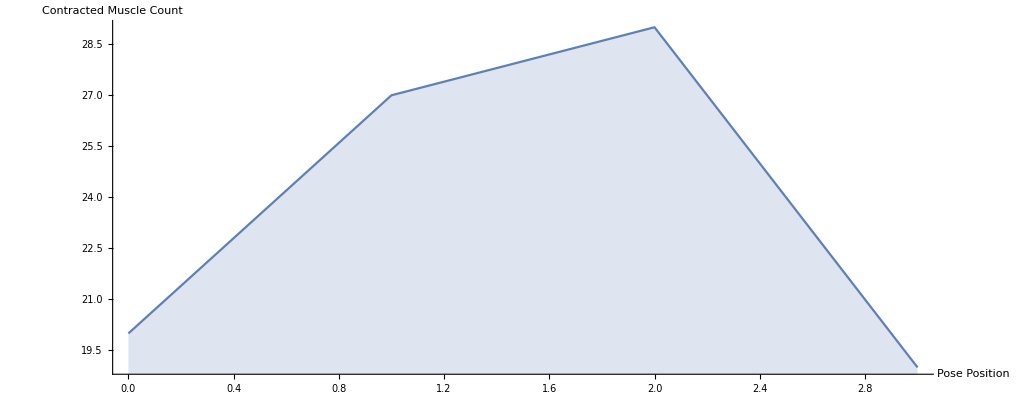
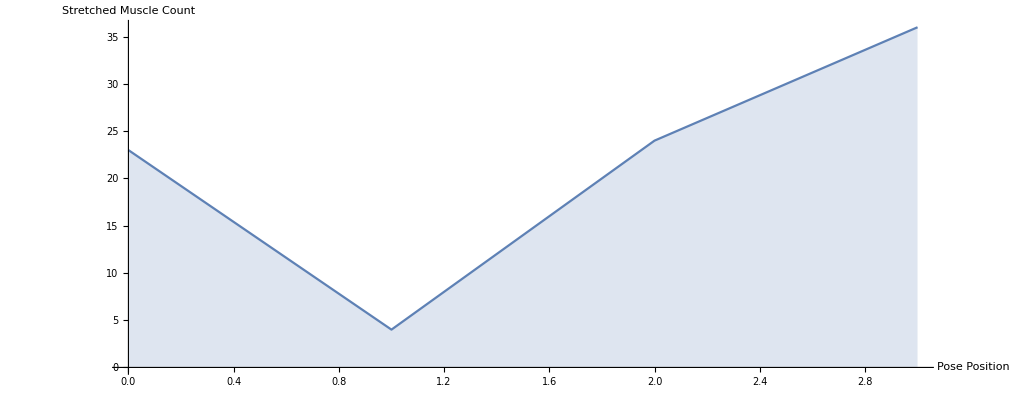
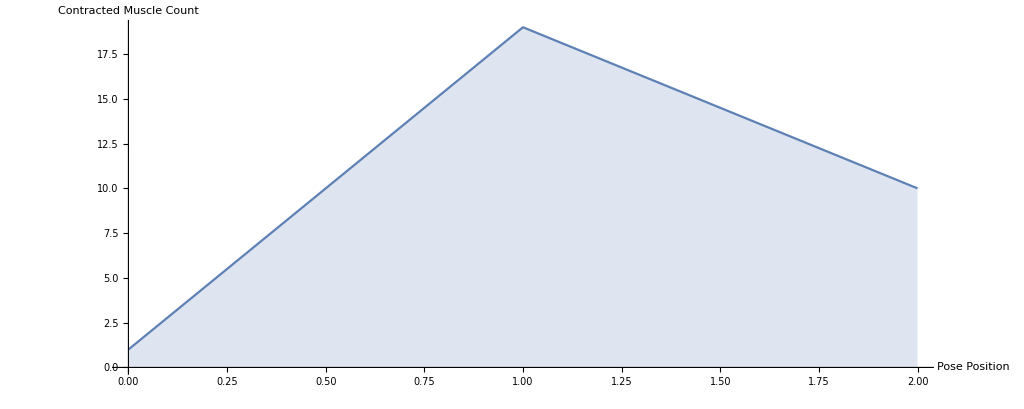
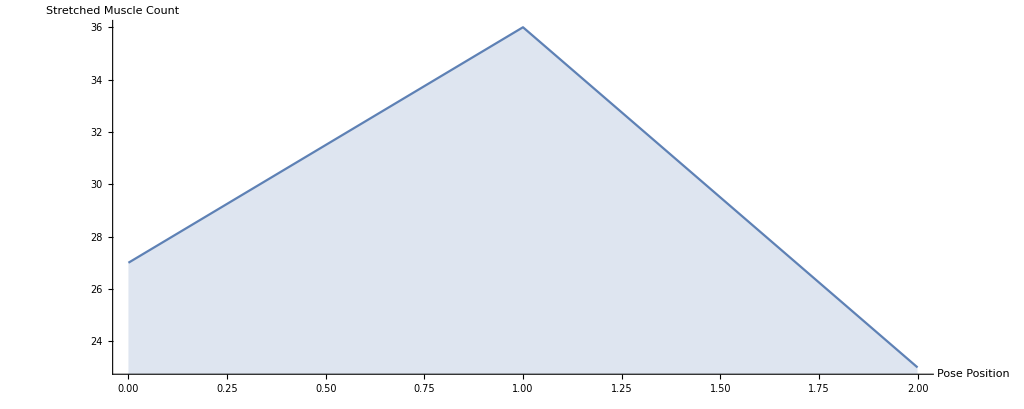
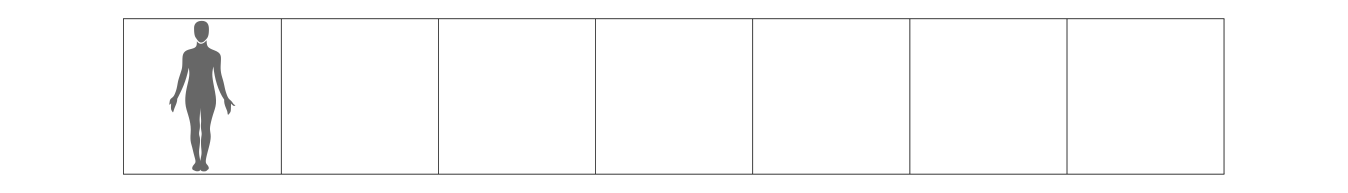
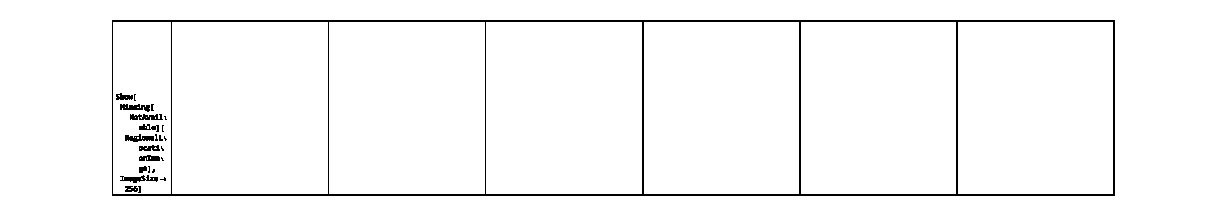
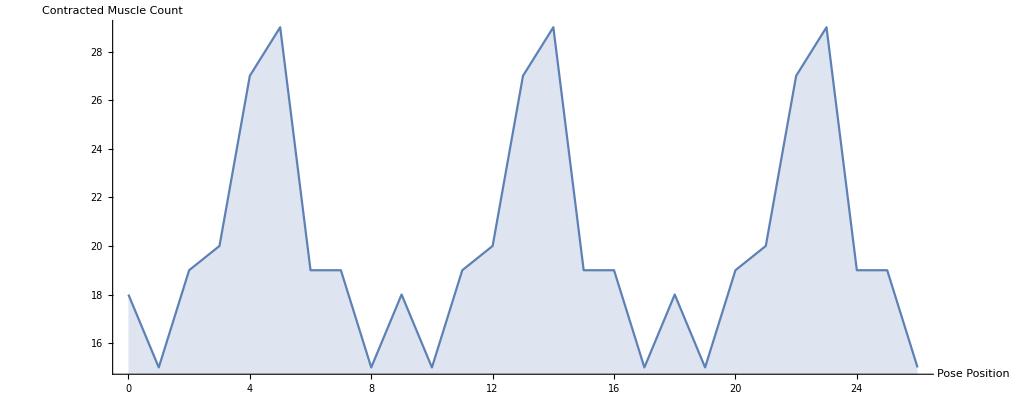
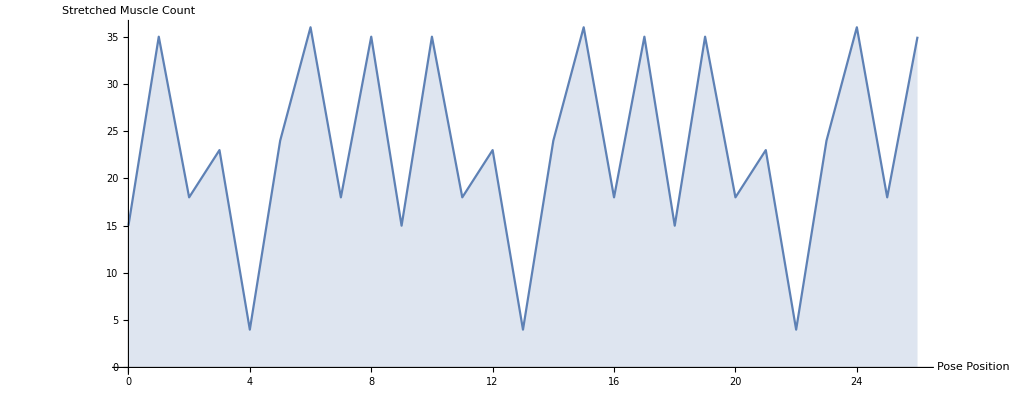
{{C1Vinyasa,{{Schematic Grid,-Graphics-},{Contracted Muscle Plot,-Graphics-},{Contracted Muscle Grid,-Graphics-},{Stretched Muscle Plot,-Graphics-},{Stretched Muscle Grid,-Graphics-}}},{C1IntegrationSeries,{{Schematic Grid,-Graphics-},{Contracted Muscle Plot,-Graphics-},{Contracted Muscle Grid,-Graphics-},{Stretched Muscle Plot,-Graphics-},{Stretched Muscle Grid,-Graphics-}}},{C1IntentionSeries,{{Schematic Grid,-Graphics-},{Contracted Muscle Plot,ListLinePlot[{14},Filling→Axis,AspectRatio→0.4,AxesLabel→{Pose Position,Contracted Muscle Count},ImageSize→1024,DataRange→{0,0}]},{Contracted Muscle Grid,-Graphics-},{Stretched Muscle Plot,ListLinePlot[{1},Filling→Axis,AspectRatio→0.4,AxesLabel→{Pose Position,Stretched Muscle Count},ImageSize→1024,DataRange→{0,0}]},{Stretched Muscle Grid,-Graphics-}}},{C1SunSalutationA,{{Schematic Grid,-Graphics-},{Contracted Muscle Plot,-Graphics-},{Contracted Muscle Grid,-Graphics-},{Stretched Muscle Plot,-Graphics-},{Stretched Muscle Grid,-Graphics-}}},{C1SunSalutationB,{{Schematic Grid,-Graphics-},{Contracted Muscle Plot,-Graphics-},{Contracted Muscle Grid,-Graphics-},{Stretched Muscle Plot,-Graphics-},{Stretched Muscle Grid,-Graphics-}}},{C1CoreSeries,{{Schematic Grid,-Graphics-},{Contracted Muscle Plot,-Graphics-},{Contracted Muscle Grid,-Graphics-},{Stretched Muscle Plot,-Graphics-},{Stretched Muscle Grid,-Graphics-}}},{C1CrescentLungeSeries,{{Schematic Grid,-Graphics-},{Contracted Muscle Plot,-Graphics-},{Contracted Muscle Grid,-Graphics-},{Stretched Muscle Plot,-Graphics-},{Stretched Muscle Grid,-Graphics-}}},{C1BalancingSeries,{{Schematic Grid,-Graphics-},{Contracted Muscle Plot,-Graphics-},{Contracted Muscle Grid,-Graphics-},{Stretched Muscle Plot,-Graphics-},{Stretched Muscle Grid,-Graphics-}}},{C1TriangleSeries,{{Schematic Grid,-Graphics-},{Contracted Muscle Plot,-Graphics-},{Contracted Muscle Grid,-Graphics-},{Stretched Muscle Plot,-Graphics-},{Stretched Muscle Grid,-Graphics-}}},{C1HipSeries,{{Schematic Grid,-Graphics-},{Contracted Muscle Plot,-Graphics-},{Contracted Muscle Grid,-Graphics-},{Stretched Muscle Plot,-Graphics-},{Stretched Muscle Grid,-Graphics-}}},{C1SpineSeries,{{Schematic Grid,-Graphics-},{Contracted Muscle Plot,-Graphics-},{Contracted Muscle Grid,-Graphics-},{Stretched Muscle Plot,-Graphics-},{Stretched Muscle Grid,-Graphics-}}},{C1SurrenderSeries,{{Schematic Grid,-Graphics-},{Contracted Muscle Plot,-Graphics-},{Contracted Muscle Grid,-Graphics-},{Stretched Muscle Plot,-Graphics-},{Stretched Muscle Grid,-Graphics-}}},{C1Series,{{Schematic Grid,-Graphics-},{Contracted Muscle Plot,-Graphics-},{Contracted Muscle Grid,-Graphics-},{Stretched Muscle Plot,-Graphics-},{Stretched Muscle Grid,-Graphics-}}}}

```mathematica
makeSquare[gr_,size_,bool_: False]:=Block[{range,magnitudes,order,padding,newRanges,res},
range=AbsoluteOptions[gr,PlotRange][[1,2]];
range=If[range=={{0,1},{0,1}},{{0,350},{0,420}},range];
magnitudes=Abs[Subtract@@@range];
order=Ordering[magnitudes,2,Greater];
padding=Subtract@@magnitudes[[order]]/2;
newRanges={{-1,1} padding+Last[range[[order]]],First[range[[order]]]};
res=Show[gr,ImageSize->size,PlotRange->Reverse@newRanges[[order]]];
If[bool,Rasterize[res],res]
];
makeSquare2[gr_,size_]:=Show[gr,ImageSize->size]

makeGrid[items_,numGridColumns_,resolution_,useMakeSquare2_]:=Block[
{gridImage, imagesLeft,numEmptyImages,images,emptyImage,allImages},
imagesLeft=Mod[Length[items],numGridColumns];
numEmptyImages=If[imagesLeft==0,0,numGridColumns-imagesLeft];

(*Make all of the images the same size*)
images=If[useMakeSquare2,makeSquare2[#,resolution],makeSquare[#,resolution]]&/@items;

emptyImage=Show[Image[{{1}}],ImageSize->resolution];

allImages=PadRight[images,Length[images]+numEmptyImages,emptyImage];

(*Lay the images out in a grid*)
gridImage=Grid[Partition[allImages,numGridColumns],Frame->All];

(*Convert the image into a form that can be copied*)
First@ImportString[ExportString[gridImage,"PDF"]]
];

posesToProperty[customYogaSequence_,property_]:=Block[
{posesOnly},
posesOnly=Map[
First[#]&,
customYogaSequence
];
Map[
#[property]&,
posesOnly
]
];

makeListLinePlot[items_,yAxisLabel_,xAxisLabel_]:=
ListLinePlot[
items[[All,-1]],
Filling->Axis,
AspectRatio->0.4,
AxesLabel->{yAxisLabel,xAxisLabel},
ImageSize->1024,
DataRange->{0,Length[items]-1}
];

getSequenceData[sequence_]:=Block[
{schematics,schematicGrid,primaryContractedMuscles,numPrimaryContractedMuscles,contractedMusclePlot,talliedContractedMuscles,highestContractedTally,mostContractedMuscles,mostContractedMusclesImages,mostContractedMusclesGrid,stretchedMuscles,numStretchedMuscles,stretchedMusclePlot,talliedStretchedMuscles,highestStretchedTally,mostStretchedMuscles,mostStretchedMusclesImages,mostStretchedMusclesGrid},
schematics = posesToProperty[sequence["FullPoseSequence"],"SimplifiedSchematic"];
schematicGrid=makeGrid[schematics,7,256,False ];

primaryContractedMuscles=posesToProperty[sequence["StandardPoseSequence"],"PrimaryContractedMuscles"];
numPrimaryContractedMuscles={}->Length[#]&/@primaryContractedMuscles;
contractedMusclePlot=makeListLinePlot[numPrimaryContractedMuscles,"Pose Position", "Contracted Muscle Count"];

talliedContractedMuscles=SortBy[Tally[Flatten[posesToProperty[sequence["StandardPoseSequence"],"PrimaryContractedMuscles"]]], Last];
highestContractedTally=Last[Last[talliedContractedMuscles]];
mostContractedMuscles=#[[1]]&/@Select[talliedContractedMuscles,Last[#]==highestContractedTally&];
mostContractedMusclesImages=DeleteCases[#["RegionalLocationImage"]&/@mostContractedMuscles,_Missing];
mostContractedMusclesGrid=makeGrid[mostContractedMusclesImages,7,256,True];

stretchedMuscles=posesToProperty[sequence["StandardPoseSequence"],"StretchedMuscles"];
numStretchedMuscles={}->Length[#]&/@stretchedMuscles;
stretchedMusclePlot=makeListLinePlot[numStretchedMuscles,"Pose Position", "Stretched Muscle Count"];

talliedStretchedMuscles=SortBy[Tally[Flatten[posesToProperty[sequence["StandardPoseSequence"],"StretchedMuscles"]]], Last];
highestStretchedTally=Last[Last[talliedStretchedMuscles]];
mostStretchedMuscles=#[[1]]&/@Select[talliedStretchedMuscles,Last[#]==highestStretchedTally&];
mostStretchedMusclesImages=DeleteCases[#["RegionalLocationImage"]&/@mostStretchedMuscles,_Missing];
mostStretchedMusclesGrid=makeGrid[mostStretchedMusclesImages,7,256,True];

{{"Schematic Grid",schematicGrid},{"Contracted Muscle Plot",contractedMusclePlot},{"Contracted Muscle Grid", mostContractedMusclesGrid},{"Stretched Muscle Plot", stretchedMusclePlot},{"Stretched Muscle Grid", mostStretchedMusclesGrid}} 
];

{#,getSequenceData[#]}&/@EntityList["CustomYogaSequence"]
```